```mathematica
(* Import data from Johns Hopkins *)
HopkinsConfirmed = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_confirmed_US.csv",CharacterEncoding->"UTF8"],1];
HopkinsDeaths = Drop[Import[NotebookDirectory[]<>"/johns-hopkins-data/time_series_covid19_deaths_US.csv",CharacterEncoding->"UTF8"],1];
StateList=AlphabeticSort[DeleteDuplicates[Transpose[HopkinsConfirmed][[7]]]];
Export[NotebookDirectory[]<>"/US-states.xls",TableForm[Table[{i,StateList[[i]]},{i,1,Length[StateList]}]],"XLS"];
```

```mathematica
(* Data for countries can be split over multiple rows in the data from Hopkins *)
DataByState = Table[{},{i,1,Length[StateList]}];
NumberOfDays = Length[Transpose[HopkinsConfirmed]]-11;

For[state = 1, state ≤ Length[StateList],state++,
TempConfirmed=Table[0,{i,1,NumberOfDays}];
TempDeaths = Table[0,{i,1,NumberOfDays}];
For[row=1,row≤ Length[HopkinsConfirmed],row++,
If[StringMatchQ[StateList[[state]], HopkinsConfirmed[[row,7]]],
(* state name of ConfirmedBystate matches current row *)
TempConfirmed = TempConfirmed + Drop[HopkinsConfirmed[[row]],11];
]
];
For[row=1,row≤ Length[HopkinsDeaths],row++,
If[StringMatchQ[StateList[[state]], HopkinsDeaths[[row,7]]],
(* state name of ConfirmedBystate matches current row *)
TempDeaths = TempDeaths + Drop[HopkinsDeaths[[row]],12];
]
];

TempConfirmedDiff=TempConfirmed-Drop[Join[{0},TempConfirmed],-1];
TempDeathsDiff=TempDeaths-Drop[Join[{0},TempDeaths],-1];
DataByState[[state]]= {ToString[StateList[[state]]],TempConfirmed,TempDeaths,TempConfirmedDiff,TempDeathsDiff};
];
(* Model *)
SIR[state_,dday_] := (
n=n0;
i=i0;
r=0;
m=0;
c=r+r+m;
s = n-i-r-m;
cost = 0;
For[sirday=1,sirday≤ dday, sirday++,
lambda = gamma * listr0[[sirday]][[2]];
ds = -lambda i *(s/n);
di = lambda i * (s/n) -gamma i - delta i;
dr = gamma i;
dm = delta i;
dc=di +dr+dm;
s+=ds;
i+=di;
r+=dr;
m+=dm;
c+=dc;
n=s+i+r;
If[sirday≤ Length[DataByState[[state]][[2]]],
cost = cost + (c-DataByState[[state]][[2]][[sirday]])^2;];
];
Return[{s,i,r,m,c,cost,di,dm}];
);
```

```mathematica
Window =3;(* Number of days over which to fit the model *)
future=30; (* Number of days to project ahead *)
```

```mathematica
StateSIR[state_] := (
Currentstate =state;
today = Length[DataByState[[Currentstate]][[2]]];
CFR=DataByState[[Currentstate]][[3]][[-1]]/(DataByState[[Currentstate]][[2]][[-1]]+1);

n0 = 10000000;
i0=100;
gamma=(1-CFR)/12.4;
delta = CFR/10.4;
listr0 = {};
For[day = 1, day <= Length[DataByState[[Currentstate]][[2]]] + 60, day++,
  listr0 = Join[listr0, {{day, 4.3}}];
  ];
(* Fit model to the data *)
For[day=1,day≤Length[DataByState[[Currentstate]][[2]]]-Window,day++,
bestr0=listr0[[day]][[2]];
bestcost=SIR[Currentstate,day+Window][[6]];
For[kr0 = 0.05,kr0≤7,kr0=kr0+0.05,
(* set this possible r0 for all folliwing days and see what the cost is *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] = kr0;];
temp=SIR[Currentstate,day + Window];
If[temp[[6]]<bestcost,bestcost=temp[[6]];bestr0=kr0;];
];

(* We found a good r0 for this day, set it for all the following days *)
For[j = 0, j <= Length[listr0] - day, j++,
listr0[[day + j]][[2]] =bestr0;];
];
(* Generate the lists of data for the plots *)
lists={};
listi={};
listr={};
listm={};
listc={};
listdi={};
listdm={};
For[day=1,day≤Length[DataByState[[Currentstate]][[2]]]+60,day++,
temp=SIR[Currentstate,day];
lists=Append[lists,{day,temp[[1]]}];
listi=Append[listi,{day,temp[[2]]}];
listr=Append[listr,{day,temp[[3]]}];
listm=Append[listm,{day,temp[[4]]}];
listc=Append[listc,{day,temp[[5]]}];
listdi=Append[listdi,{day,temp[[7]]}];
listdm=Append[listdm,{day,temp[[8]]}];
];
Return[{Currentstate,DataByState[[Currentstate]][[1]],listr0}];
);
```

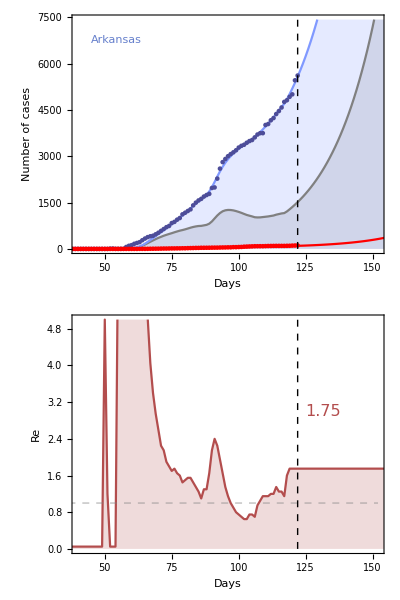

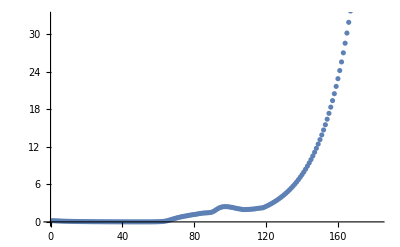

```mathematica
(* Fit model for this state *)
StateSIR[5];

(* Generate plots *)
height=Max[ {Max[Drop[listc,-55]],Max[DataByState[[Currentstate]][[2]]]}];

If[listr0[[-1]][[2]]<0.8,R0Color=RGBColor[0.3,0.7,0.3],If[listr0[[-1]][[2]]>1.2,R0Color=RGBColor[0.7,0.3,0.3],R0Color=RGBColor[0.9,0.7,0.3]]];

plotFinalR0 = Graphics[{Text[Style[listr0[[-1]][[2]], FontSize->16,R0Color],{today+3,3},{Left,Center}]}];

plotLine = Graphics[Style[Line[{{0, 1}, {today+future, 1}}],Dashed,RGBColor [0.5,0.5,0.5,0.5]]];

plotstatename = Graphics[{Text[Style[DataByState[[Currentstate]][[1]], Large,RGBColor[0.4,0.5,0.8]],{45,1.00height},{Left,Center}]}];

plotModel=Show[{ListPlot[{listi,listc,DataByState[[Currentstate]][[2]],DataByState[[Currentstate]][[3]],listm},PlotRange->{{40,today+future},{0,1.10height}},Joined->{True,True,False,False,True},Filling->{1-> Bottom,2->Bottom},PlotStyle->{Gray,RGBColor[0.5,0.6,1],RGBColor[0.3,0.3,0.6],Red,Red},FrameLabel->{"Days","Number of cases"},Frame->True,FrameTicks->Automatic,FrameStyle->Directive[Thickness[0.002],13],AspectRatio->1/1,ImageSize->600],plotstatename}];

plotR0=ListPlot[listr0,Joined->True,Filling->{1->Bottom},PlotStyle->R0Color,FrameLabel->{"Days","Re"},FrameStyle->Directive[Thickness[0.002],13],Frame->True,FrameTicks->Automatic,AspectRatio->1/8,PlotRange->{{40,today+future},{0,5}},ImageSize->600];

ThePlotThickens=Multicolumn[{Show[{plotModel,Graphics[{Dashed, Line[{{today, 0}, {today, 1.2 height}}]}]},ImagePadding->{{70,10},{20,10}}],Show[{plotR0,plotFinalR0,plotLine,Graphics[{Dashed, Line[{{today, 0}, {today, 7}}]}]},ImagePadding->{{70,10},{40,5}}]},1]

stateFilename=NotebookDirectory[]<>"/results/SIR-US-" <> ToString[DataByState[[Currentstate]][[1]]] <> "-" <> DateString[{"ISODate"}] <> ".png";

Export[stateFilename, ThePlotThickens, ImageResolution -> 600];

ListPlot[listdm]
```

```mathematica
R0PerState={};
For[state=1,state≤Length[StateList],state++,
R0PerState = Append[R0PerState,StateSIR[state]];
Print["State: "<>R0PerState[[-1]][[2]]<>" -> "<>ToString[R0PerState[[-1]][[3]][[-1]][[2]]]];
]
```

State: Alabama -> 1.38

State: Alaska -> 0.96

State: American Samoa -> 0.02

State: Arizona -> 1.12

State: Arkansas -> 1.76

State: California -> 1.22

State: Colorado -> 0.92

State: Connecticut -> 0.88

State: Delaware -> 1.02

State: Diamond Princess -> 0.02

State: District of Columbia -> 1.08

State: Florida -> 1.14

State: Georgia -> 1.16

State: Grand Princess -> 0.02

State: Guam -> 2.52

State: Hawaii -> 0.3

State: Idaho -> 1.14

State: Illinois -> 1.08

State: Indiana -> 1.06

State: Iowa -> 1.

State: Kansas -> 0.86

State: Kentucky -> 0.9

State: Louisiana -> 1.34

State: Maine -> 1.56

State: Maryland -> 1.22

State: Massachusetts -> 0.8

State: Michigan -> 0.96

State: Minnesota -> 1.3

State: Mississippi -> 1.16

State: Missouri -> 0.9

State: Montana -> 1.04

State: Nebraska -> 0.96

State: Nevada -> 1.12

State: New Hampshire -> 1.14

State: New Jersey -> 0.72

State: New Mexico -> 1.04

State: New York -> 0.62

State: North Carolina -> 1.48

State: North Dakota -> 1.66

State: Northern Mariana Islands -> 1.

State: Ohio -> 1.08

State: Oklahoma -> 1.16

State: Oregon -> 0.82

State: Pennsylvania -> 0.92

State: Puerto Rico -> 1.3

State: Rhode Island -> 0.98

State: South Carolina -> 1.12

State: South Dakota -> 0.84

State: Tennessee -> 1.02

State: Texas -> 1.08

State: Utah -> 1.14

State: Vermont -> 0.58

State: Virgin Islands -> 0.02

State: Virginia -> 1.2

State: Washington -> 0.82

State: West Virginia -> 1.72

State: Wisconsin -> 1.34

State: Wyoming -> 0.92

```mathematica
stateplotted = {};
For[state=1,state≤Length[StateList],state++,
stateplotted=Append[stateplotted,Entity["AdministrativeDivision",StringReplace[ToString[StateList[[state]]]," " -> ""]]->R0PerState[[state]][[3]][[-1]][[2]]];
];
```

```mathematica
USMap = GeoRegionValuePlot[stateplotted,ImageSize->Large,ColorFunction->Function[{z},ColorData["TemperatureMap"][z/2]],ColorFunctionScaling->False,ImageSize->Full]
```

-Graphics-

```mathematica
stateMapFilename=NotebookDirectory[]<>"/results/SIR-US-map-" <> DateString[{"ISODate"}] <> ".png";
Export[stateMapFilename, USMap, ImageResolution -> 600];
```